```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Problem 2 *)

(* Kinetic and Potential Energies around the cart mass and pendulum mass *)
T=1/2 M Yt^2+1/2 m (yt^2+zt^2);
V=m g z;
(* External forcing. Assumes a solution of y = Ye^ⅈωt, θ = Θe^ⅈωt, F = F0 e^ⅈωt and the e^ⅈωt 
drops out when calculating the particular solution *)
f = {{F0},{0}};
(* Torque done by the damper at the origin *)
τ=c θt;
(* Positions *)
y=Y+l Sin[θ];z=-l Cos[θ];
yt=Yt+l Cos[θ] θt;zt=l Sin[θ] θt;

parameters={m->1,M->10,l->1,g->981/100, c->4};
```

```mathematica
T
V
f
```

1/2 m (θt^2 l^2 sin^2(θ)+(θt l cos(θ)+Yt)^2)+(M Yt^2)/2

-g l m cos(θ)

(F0
0)

```mathematica
(*First E-L equation, Y*)
L=T-V;
D[L,Yt];
D[%,Y] Yt+D[%,Yt] Ytt+D[%,θ] θt+D[%,θt] θtt;
D[L,Y];
eqn1=Collect[%%-%,{Ytt,θtt},Simplify]
```

θt^2 (-l) m sin(θ)+θtt l m cos(θ)+Ytt (m+M)

```mathematica
(*Second E-L equation, θ *)
D[L,θt];
D[%,Y] Yt+D[%,Yt] Ytt+D[%,θ] θt+D[%,θt] θtt;
D[L,θ];
eqn2=Collect[%%-%,{Ytt,θtt},Simplify]+ τ
```

c θt+g l m sin(θ)+θtt l^2 m+l m Ytt cos(θ)

```mathematica
(*Linearize first E-L equation. Trigonometric simplifications*)
eqn1/.{Cos[θ]->1,Sin[θ]->θ}
% /. {θt^2 ->0};
leqn1 = Simplify[%]
```

θ θt^2 (-l) m+θtt l m+Ytt (m+M)

θtt l m+Ytt (m+M)

```mathematica
(*Linearize second E-L equation. Trigonometric simplifications*)
eqn2/.{Cos[θ]->1,Sin[θ]->θ}
leqn2= Simplify[%]
```

c θt+g θ l m+θtt l^2 m+l m Ytt

c θt+l m (g θ+Ytt)+θtt l^2 m

```mathematica
(* Assuming y = Ye^ⅈωt, θ = Θe^ⅈωt, where s = ⅈω, take derivatives and plug in. *)
nleqn1 = Collect[leqn1/.{Ytt->s^2 Y,θ->Θ,θt->s Θ,θtt->s^2 Θ},{Y,Θ},Simplify]
nleqn2 =Collect[leqn2/.{Ytt->s^2Y,θ->Θ,θt->s Θ,θtt->s^2 Θ},{Y,Θ},Simplify]
```

Θ l m s^2+s^2 Y (m+M)

Θ (s (c+l^2 m s)+g l m)+l m s^2 Y

```mathematica
(* Create coefficient matrix *)
A = {{nleqn1[[1]] /. {Y ->1},  nleqn1[[2]] /. {Θ->1}},
{nleqn2[[1]] /. {Y->1}, nleqn2[[2]] /. {Θ->1}}}
```

((m+M) s^2 | l m s^2
l m s^2 | g l m+s (m s l^2+c))

```mathematica
(* Characteristic polynomial *)
cp=Collect[Det[A],w,Simplify]
```

s^2 (s (c (m+M)+l^2 m M s)+g l m (m+M))

```mathematica
(* Solve for eigenvalue *)
soln=Solve[cp ==0,s]
```

{{s→0},{s→0},{s→(-√(m+M) √(c^2 m+c^2 M-4 g l^3 m^2 M)-c m-c M)/(2 l^2 m M)},{s→(√(m+M) √(c^2 m+c^2 M-4 g l^3 m^2 M)-c m-c M)/(2 l^2 m M)}}

```mathematica
(* Plug in parameters, solve for eigenvalue *)
s1 = soln[[3,1]] /.parameters
s2 = soln[[4,1]]/.parameters
```

s→1/20 (-44-ⅈ √(11902/5))

s→1/20 (-44+ⅈ √(11902/5))

```mathematica
(* Since s = ⅈω, solve for ω1*)
w1 = (-45000-4500 ⅈ √9710)/225000/ I
```

-(ⅈ (-45000-4500 ⅈ √9710))/225000

```mathematica
(* Since s = ⅈω, solve for ω2*)
w2 = (-45000+4500 ⅈ √9710)/225000 / I
```

-(ⅈ (-45000+4500 ⅈ √9710))/225000

```mathematica
(* Take the inverse of coefficient matrix, plug in parametes, multiply with forcing function
  to get displacement amplitudes Y and Θ *)
(Inverse[A] /.parameters) . f
```

((F0 (s (s+4)+981/100))/(10 s^4+44 s^3+(10791 s^2)/100)
-(F0 s^2)/(10 s^4+44 s^3+(10791 s^2)/100))

```mathematica
(* Multiply Y and Θ by e^ⅈωt to get y and θ *)
Yfunc = Simplify[(((Inverse[A].f /. parameters) Exp[s t] /. {s-> I wf}))[[1,1]]]
Θfunc = Simplify[(((Inverse[A].f /. parameters)Exp[s t]/. {s-> I wf}))[[2,1]]]
```

-(F0 (100 wf^2-400 ⅈ wf-981) ⅇ^(ⅈ t wf))/(wf^2 (1000 wf^2-4400 ⅈ wf-10791))

-(100 F0 ⅇ^(ⅈ t wf))/(-1000 wf^2+4400 ⅈ wf+10791)

```mathematica
ComplexExpand[Yfunc]
```

(40000 F0 wf sin(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)+(300100 F0 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(10585971 F0 cos(t wf))/((19360000 wf^2+(1000 wf^2-10791)^2) wf^2)+ⅈ (-(100000 F0 wf^2 sin(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)+(300100 F0 sin(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(10585971 F0 sin(t wf))/((19360000 wf^2+(1000 wf^2-10791)^2) wf^2)-(40000 F0 wf cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2))

```mathematica
ComplexExpand[Θfunc]
```

-(440000 F0 wf sin(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)+(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)-(1079100 F0 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)+ⅈ ((100000 F0 wf^2 sin(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)-(1079100 F0 sin(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)+(440000 F0 wf cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2))

```mathematica
(* Particular solution = real parts of y and θ *)
yp = {(40000 F0 wf Sin[t wf])/(19360000 wf^2+(1000 wf^2-10791)^2)-(100000 F0 wf^2 Cos[t wf])/(19360000 wf^2+(1000 wf^2-10791)^2)+(300100 F0 Cos[t wf])/(19360000 wf^2+(1000 wf^2-10791)^2)-(10585971 F0 Cos[t wf])/((19360000 wf^2+(1000 wf^2-10791)^2) wf^2),-(440000 F0 wf Sin[t wf])/(19360000 wf^2+(10791-1000 wf^2)^2)+(100000 F0 wf^2 Cos[t wf])/(19360000 wf^2+(10791-1000 wf^2)^2)-(1079100 F0 Cos[t wf])/(19360000 wf^2+(10791-1000 wf^2)^2)}
```

{(40000 F0 wf sin(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)+(300100 F0 cos(t wf))/(19360000 wf^2+(1000 wf^2-10791)^2)-(10585971 F0 cos(t wf))/((19360000 wf^2+(1000 wf^2-10791)^2) wf^2),-(440000 F0 wf sin(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)+(100000 F0 wf^2 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)-(1079100 F0 cos(t wf))/(19360000 wf^2+(10791-1000 wf^2)^2)}

```mathematica
Clear[F0, wf]
```

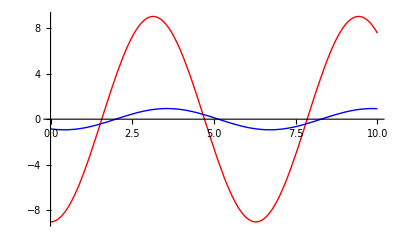

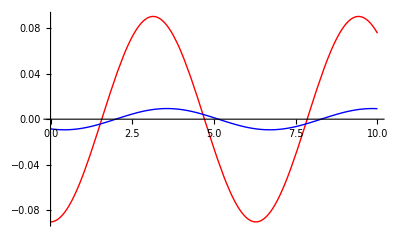

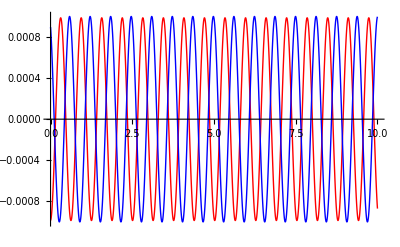

```mathematica
(* High F0 -> big amplitude. Low F0 -> low amplitude *)
(* Low wf -> Pendulum translates with cart, low angular displacement.
High wf -> Pendulum angular displacement increases, out of phase. *)
(* Red = cart. Blue = pendulum *)
F0 = 100;
wf=1;
Plot[yp , {t,0,10}, PlotStyle->{Red, Blue}]
F0 = 1;
Plot[yp , {t,0,10}, PlotStyle->{Red, Blue}]
wf = 10;
Plot[yp , {t,0,10}, PlotStyle->{Red, Blue}]
```

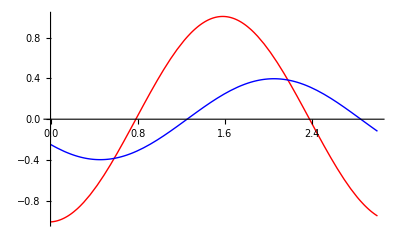

{-0.396895,{t→0.455747}}

```mathematica
(* To find limits on amplitude and frequency, find F0 and ωf for θ being small 
(less than .4 radians or 23 degrees *)
(* Displacement is biggest when wf = the natural frequency. So assume wf = ω1, ω2 (real part) *)
(* All this assumes a damping c = 1 *)
F0 = 44;  (* Newtons *)
wf = (4500  √9710)/225000;
Plot[yp , {t,0,3}, PlotStyle->{Red, Blue}]
FindMinimum[yp[[2]], {t, 1}]
```